```mathematica
(*As a first approximation, the resonance periods Tn of the moonpool, in s, may be evaluated as follows*)
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
l=26.2;
b=26.2;
```

```mathematica
λ[n_]:=n*π/l;
(*n/(b*l^2)*NIntegrate[(Cos[λ[n]*x1]*Cos[λ[n]*x2])/Sqrt[(x1-x2)^2+(y1-y2)^2],{y1,0,b},{y2,0,b}]
J[n_]:=n/(b*l^2)*NIntegrate[(Cos[λ[n]*x1]*Cos[λ[n]*x2])/Sqrt[(x1-x2)^2+(y1-y2)^2],{y1,0,b},{y2,0,b},{x1,0,l},{x2,0,l}]*)
```

```mathematica
J[n_,r_(*r=b/l*)]:=Module[{θ},
θ=ArcTan[1/r];
2/(n*π^2*r)*(NIntegrate[r^2/(u^2*Sqrt[u^2+r^2])*(1+(u-1)*Cos[n*π*u]-Sin[n*π*u]/(n*π)),{u,0,1}]+1/Sin[θ]-1)]
```

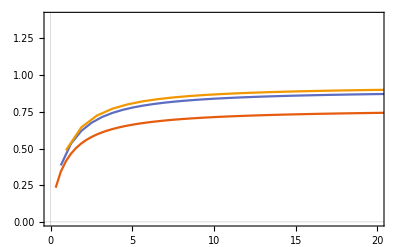

```mathematica
ListPlot[
{Table[{1*π*r,J[1,r]},{r,0.1,10,0.1}],
Table[{2*π*r,J[2,r]},{r,0.1,10,0.1}],
Table[{3*π*r,J[3,r]},{r,0.1,10,0.1}]}
,PlotTheme->"Scientific"
,PlotRange->{{0,20},{0,1.4}}
,Joined->True
]
```

```mathematica
h=7.5;
g=9.81;
w[n_]:=Module[{r},
r=b/l;
Sqrt[g*λ[n]*(1+J[n,r]*Tanh[λ[n]*h])/(J[n,r]+Tanh[λ[n]*h])]];
T[n_]:=2π/w[n]
```

```mathematica
Table[{n,T[n]},{n,1,5}]
```

{{1,5.56518},{2,4.08419},{3,3.34363},{4,2.8965},{5,2.5908}}

```mathematica
H=7.5;
Table[{n,2π*Sqrt[(g*π/l)*Tanh[H*π/l]]},{n,1,5}]
```

{{1,5.76612},{2,5.76612},{3,5.76612},{4,5.76612},{5,5.76612}}

reference
-Graphics-